```mathematica
ClearAll["Global`*"];
orthog[m_,n_]:=
Module[{nn=n,mm=m,σ,a,b,Ja,w,xi,eval,evec,esys},
σ=Table[0.,{i,1,2nn},{j,1,2nn}];
Do[σ[[2,i+1]]=mm[[i+1]],{i,0,2nn-1}];

a=Table[0.,{i,1,nn}];b=a;
a[[1]]=mm[[2]]/mm[[1]];
b[[1]]=0;

Do[
Do[
σ[[i+2,j+1]]=σ[[i+1,j+2]]-a[[i]]σ[[i+1,j+1]]-b[[i]]σ[[i,j+1]];
a[[i+1]]=-σ[[i+1,i+1]]/σ[[i+1,i]]+σ[[i+2,i+2]]/σ[[i+2,i+1]];
b[[i+1]]=σ[[i+2,i+1]]/σ[[i+1,i]];
,{j,i,2nn-i-1}];
,{i,1,nn-1}];

Ja=DiagonalMatrix[a];
Do[
Ja[[i,i+1]]=-Sqrt[Abs[b[[i+1]]]];
Ja[[i+1,i]]=-Sqrt[Abs[b[[i+1]]]];
,{i,1,nn-1}];

esys=Eigensystem[Ja];
eval=esys[[1]];evec=esys[[2]];

w=Table[evec[[i,1]]^2 mm[[1]],{i,1,nn}];
{eval,w}
];
```

```mathematica
(* Physical parameters *)
γ=1;
Rey=10000;
Ca=1;
Cp=1;

(* Get weights and abscissa in Ro direction *)
nro=2;

(*μRo=0.0;
σRo=0.2;
RoPDF=LogNormalDistribution[μRo,σRo];*)

μRo=1.;
σRo=0.2;
RoPDF=NormalDistribution[μRo,σRo];

momRo[l_]:=Moment[RoPDF,l];
momRos=Table[momRo[l],{l,0,2nro-1}];

(* Get fixed weights and nodes in Ro direction *)
{Ros,wRos}=orthog[momRos,nro];

Do[
μR[l]=PDF[RoPDF,x]/.{x->Ros[[l]]}//N;
σR[l]=0.2;
μRd[l]=0.1;
σRd[l]=0.1;
ρRRd[l]=0.0;
RRdPDF[l]=BinormalDistribution[{μR[l],μRd[l]},{σR[l],σRd[l]},ρRRd[l] ];
,{l,1,nro}];

momRRd[i_,j_,l_]:=Moment[RRdPDF[l],{i,j}];

nr=2;
nrd=2;
ks=Flatten[Table[Flatten[{Table[{q,p,r},{q,0,nr-1},{p,0,2nrd-1}],
Table[{q,p,r},{q,nr,2nr-1},{p,0,0}]}
,2],{r,0,nro-1}],1];

(* gets total moments in {lmn} from conditional moments on {lm} plus Ro directions *)
ic=Table[Sum[wRos[[l]] Ros[[l]]^ks[[i,3]] momRRd[ks[[i,1]],ks[[i,2]],l],{l,1,nro}],{i,1,Length[ks]}];
moms=ic;

rhs[mom_]:=
Module[{kk=ks,moms=mom,rhs,l,m,n},
rhs={};
Do[
l=kk[[i,1]];
m=kk[[i,2]];
n=kk[[i,3]];
AppendTo[rhs,
l mom[l-1,m+1,n]-m(4/Rey mom[l,m,n-2]+2 γ Ca mom[l+1,m-1,n-2]+Cp mom[l,m-1,n-1])];
,{i,1,Length[ks]}];
rhs
];

(*rhs[mom_]:=
Table[
ks[[i,1]] mom[ks[[i,1]]-1,ks[[i,2]]+1,ks[[i,3]]]-ks[[i,2]](4/Rey mom[ks[[i,1]],ks[[i,2]],ks[[i,3]]-2]+2 γ Ca mom[ks[[i,1]]+1,ks[[i,2]]-1,ks[[i,3]]-2]+Cp mom[ks[[i,1]],ks[[i,2]]-1,ks[[i,3]]-1])
,{i,1,Length[ks]}];*)


dt=1 10^-4;
Nt=1000;
sol={};
AbsoluteTiming[
Do[
AppendTo[sol,moms];

(* converts vector of total M_lmn to M_lm @ each R_o,k *)
eqns=Table[moms[[i]]==Sum[wRos[[l+1]] Ros[[l+1]]^ks[[i,3]] pm[ks[[i,1]],ks[[i,2]],l]
,{l,0,nro-1}],{i,1,Length[ks]}];
vars=DeleteDuplicates[Flatten[Table[pm[ks[[i,1]],ks[[i,2]],l],{l,0,nro-1},{i,1,Length[ks]}]]];

Print[AbsoluteTiming[
linsolv=First[vars/.Solve[eqns,vars]];
(* conditioned moments *)
mymom[q_,p_,r_]:=linsolv[[First[First[Position[ks,{q,p,r}]]]]];
]];

Print[AbsoluteTiming[
Do[
(* get conditional moments at specific Ro_l location for index l *)
mRs=Table[mymom[i,0,l-1],{i,0,2nr-1}];
{xi[l],w}=orthog[mRs,nr];
v=Table[
Table[(xi[l][[i]])^j,{i,1,nr}]
,{j,0,nr-1}];
r1=DiagonalMatrix[w];
Do[ms[m]=Table[mymom[i,m,l-1],{i,0,nr-1}],{m,0,2nrd-1}];
Do[condmoms[i]=LinearSolve[v.r1,ms[i]],{i,0,2nrd-1}];
Do[condmomvec[j]=Table[condmoms[i][[j]],{i,0,2nrd-1}];,{j,1,nr}];
Do[
{xis[l][i],ws[i]}=orthog[condmomvec[i],nrd];
,{i,1,nr}];
Do[wtot[l][j,i]=w[[j]]ws[j][[i]],{i,1,nrd},{j,1,nr}];
,{l,1,nro }];
]];

(* note that in mom[p,q,l], l is the Ro index and p and q are moment exponents! *)
mom[p_,q_,l_]:=Sum[wtot[l][j,i](xi[l][[j]])^p(xis[l][j][[i]])^q,{i,1,nrd},{j,1,nr}];
(* turns conditional moments into total moments *)
momtot[p_,q_,r_]:=Sum[wRos[[l]] Ros[[l]]^r mom[p,q,l],{l,1,nro}];

Print[AbsoluteTiming[
myrhs=rhs[momtot];
]];
moms=moms+dt myrhs;
If[Norm[moms]>10^3,
Break[];
Print["Crash"];
];
,{ts,1,1+0Nt}];
]
```

{0.000902,Null}

{0.001525,Null}

{0.008138,Null}

{0.011223,Null}

```mathematica
NSolve[eqns,vars]//AbsoluteTiming
```

{0.000962,{{pm[0,0,0]→1.,pm[0,1,0]→0.1,pm[0,2,0]→0.02,pm[0,3,0]→0.004,pm[1,0,0]→1.20985,pm[1,1,0]→0.120985,pm[1,2,0]→0.0241971,pm[1,3,0]→0.00483941,pm[2,0,0]→1.50375,pm[3,0,0]→1.9161,pm[0,0,1]→1.,pm[0,1,1]→0.1,pm[0,2,1]→0.02,pm[0,3,1]→0.004,pm[1,0,1]→1.20985,pm[1,1,1]→0.120985,pm[1,2,1]→0.0241971,pm[1,3,1]→0.00483941,pm[2,0,1]→1.50375,pm[3,0,1]→1.9161}}}

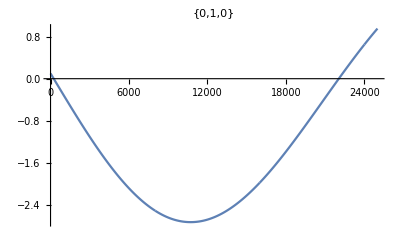
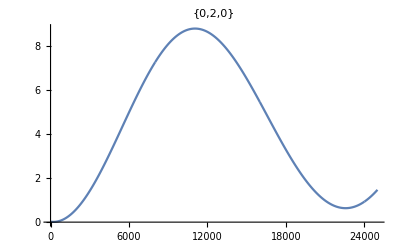
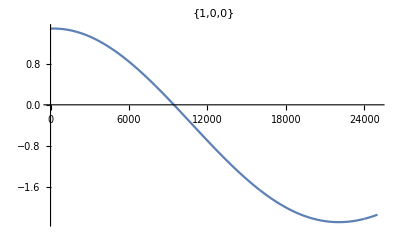
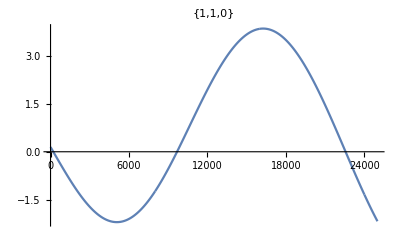
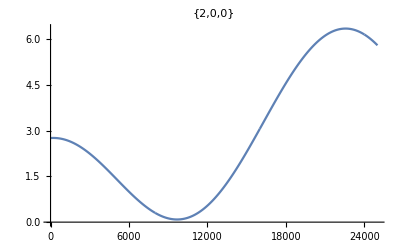
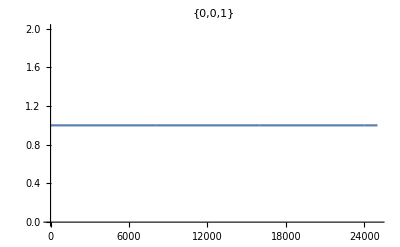
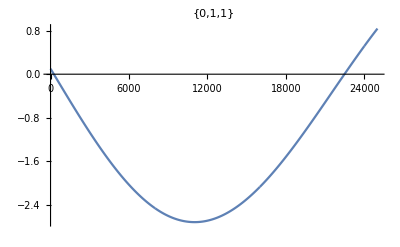
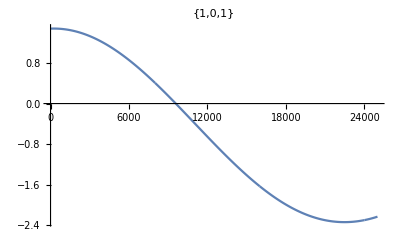

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<3&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[sol[[All,i]],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
],
{i,1,Length[moms]}]
plots
```

```mathematica
(* euler *)
(*Do[
AppendTo[sol,moms];
AppendTo[solexact,moms2];

mymom[q_,p_,r_]:=moms[[First[First[Position[ks,{q,p,r}]]]]];
mymomex[q_,p_,r_]:=moms2[[First[First[Position[ks,{q,p,r}]]]]];
Do[
mRs=Table[mymom[i,0,0],{i,0,2nr-1}];
{xi[l],w}=orthog[mRs,nr];
v=Table[
Table[(xi[l][[i]])^j,{i,1,nr}]
,{j,0,nr-1}];
r1=DiagonalMatrix[w];
Do[ms[m]=Table[mymom[i,m,0],{i,0,nr-1}],{m,0,2nrd-1}];
Do[condmoms[i]=LinearSolve[v.r1,ms[i]],{i,0,2nrd-1}];
Do[condmomvec[j]=Table[condmoms[i][[j]],{i,0,2nrd-1}];,{j,1,nr}];
Do[
{xis[l][i],ws[i]}=orthog[condmomvec[i],nrd];
,{i,1,nr}];
Do[wtot[l][j,i]=w[[j]]ws[j][[i]],{i,1,nrd},{j,1,nr}];
,{l,1,nro }];
mom[l_][p_,q_]:=Sum[wtot[l][j,i](xi[l][[j]])^p(xis[l][j][[i]])^q,{i,1,nrd},{j,1,nr}];
momtot[p_,q_,r_]:=Sum[wRos[[l]] Ros[[l]]^r mom[l][p,q],{l,1,nro}];

moms=moms+dt rhs[momtot];
moms2=moms2+dt rhs0[mymomex];
,{ts,1,Nt}];*)
(* rk2 *)
(*Do[
AppendTo[sol,moms];
AppendTo[solexact,moms2];

mymom[q_,p_,r_]:=moms[[First[First[Position[ks,{q,p,r}]]]]];
mymomex[q_,p_,r_]:=moms2[[First[First[Position[ks,{q,p,r}]]]]];
Do[
mRs=Table[mymom[i,0,0],{i,0,2nr-1}];
{xi[l],w}=orthog[mRs,nr];
v=Table[
Table[(xi[l][[i]])^j,{i,1,nr}]
,{j,0,nr-1}];
r1=DiagonalMatrix[w];
Do[ms[m]=Table[mymom[i,m,0],{i,0,nr-1}],{m,0,2nrd-1}];
Do[condmoms[i]=LinearSolve[v.r1,ms[i]],{i,0,2nrd-1}];
Do[condmomvec[j]=Table[condmoms[i][[j]],{i,0,2nrd-1}];,{j,1,nr}];
Do[
{xis[l][i],ws[i]}=orthog[condmomvec[i],nrd];
,{i,1,nr}];
Do[wtot[l][j,i]=w[[j]]ws[j][[i]],{i,1,nrd},{j,1,nr}];
,{l,1,nro }];
mom[l_][p_,q_]:=Sum[wtot[l][j,i](xi[l][[j]])^p(xis[l][j][[i]])^q,{i,1,nrd},{j,1,nr}];
momtot[p_,q_,r_]:=Sum[wRos[[l]] Ros[[l]]^r mom[l][p,q],{l,1,nro}];

y1=moms+dt/2 rhs[momtot];
yex=moms2+dt/2 rhs0[mymomex];

mymomex[q_,p_,r_]:=yex[[First[First[Position[ks,{q,p,r}]]]]];
mymom[q_,p_,r_]:=y1[[First[First[Position[ks,{q,p,r}]]]]];
(* stage 2 *)
Do[
mRs=Table[mymom[i,0,0],{i,0,2nr-1}];
{xi[l],w}=orthog[mRs,nr];
v=Table[
Table[(xi[l][[i]])^j,{i,1,nr}]
,{j,0,nr-1}];
r1=DiagonalMatrix[w];
Do[ms[m]=Table[mymom[i,m,0],{i,0,nr-1}],{m,0,2nrd-1}];
Do[condmoms[i]=LinearSolve[v.r1,ms[i]],{i,0,2nrd-1}];
Do[condmomvec[j]=Table[condmoms[i][[j]],{i,0,2nrd-1}];,{j,1,nr}];
Do[
{xis[l][i],ws[i]}=orthog[condmomvec[i],nrd];
,{i,1,nr}];
Do[wtot[l][j,i]=w[[j]]ws[j][[i]],{i,1,nrd},{j,1,nr}];
,{l,1,nro }];
mom[l_][p_,q_]:=Sum[wtot[l][j,i](xi[l][[j]])^p(xis[l][j][[i]])^q,{i,1,nrd},{j,1,nr}];
momtot[p_,q_,r_]:=Sum[wRos[[l]] Ros[[l]]^r mom[l][p,q],{l,1,nro}];

moms=moms+dt rhs[momtot];
moms2=moms2+dt rhs0[mymomex];
,{ts,1,Nt}];*)
```